```mathematica
Clear[i]
Clear[μ]
Clear[θ1]
Clear[θ2]
Clear[θ3]

SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])

zero={{1},{0}};
one={{0},{1}};
ρGHZ= (1/(√2)(KroneckerProduct[zero,zero,zero]+ KroneckerProduct[one,one,one])).(1/(√2)(KroneckerProduct[zero,zero,zero]+ KroneckerProduct[one,one,one]))†;
ρW = (1/(√3)(KroneckerProduct[zero,zero,one]+ KroneckerProduct[zero,one,zero]+KroneckerProduct[one,zero,zero])).(1/(√3)(KroneckerProduct[zero,zero,one]+ KroneckerProduct[zero,one,zero]+KroneckerProduct[one,zero,zero]))†;

ρWExp ={{0.0182+0.0000 I,0.0102-0.0026 I,0.0186+0.0041 I,-0.0138-0.0114 I,0.0224+0.0084 I,-0.0012-0.0030 I,-0.0031-0.0065 I,-0.0028-0.0095 I},{0.0102+0.0026 I,0.3447+0.0000 I,0.3148-0.0117 I,0.0152-0.0010 I,0.2973-0.0320 I,0.0171+0.0330 I,0.0516+0.0081 I,0.0146-0.0094 I},{0.0186-0.0041 I,0.3148+0.0117 I,0.2956+0.0000 I,0.0035-0.0014 I,0.2850-0.0181 I,0.0112+0.0296 I,0.0423+0.0073 I,0.0084-0.0117 I},{-0.0138+0.0114 I,0.0152+0.0010 I,0.0035+0.0014 I,0.0327+0.0000 I,-0.0002+0.0041 I,-0.0023+0.0013 I,0.0131+0.0011 I,0.0083+0.0034 I},{0.0224-0.0084 I,0.2973+0.0320 I,0.2850+0.0181 I,-0.0002-0.0041 I,0.2814+0.0000 I,0.0044+0.0303 I,0.0366+0.0082 I,0.0043-0.0120 I},{-0.0012+0.0030 I,0.0171-0.0330 I,0.0112-0.0296 I,-0.0023-0.0013 I,0.0044-0.0303 I,0.0089+0.0000 I,0.0038-0.0036 I,0.0027-0.0009 I},{-0.0031+0.0065 I,0.0516-0.0081 I,0.0423-0.0073 I,0.0131-0.0011 I,0.0366-0.0082 I,0.0038+0.0036 I,0.0123+0.0000 I,0.0061-0.0009 I},{-0.0028+0.0095 I,0.0146+0.0094 I,0.0084+0.0117 I,0.0083-0.0034 I,0.0043+0.0120 I,0.0027+0.0009 I,0.0061+0.0009 I,0.0063+0.0000 I}};




IdExp={{0.1657+0.0000 I,0.0192+0.0063 I,0.0107+0.0078 I,-0.0037+0.0010 I,0.0035+0.0050 I,0.0008-0.0029 I,0.0041+0.0039 I,-0.0066-0.0014 I},{0.0192-0.0063 I,0.1181+0.0000 I,0.0039-0.0001 I,0.0059+0.0062 I,0.0029-0.0018 I,0.0116+0.0072 I,-0.0079-0.0003 I,0.0032+0.0001 I},{0.0107-0.0078 I,0.0039+0.0001 I,0.1421+0.0000 I,0.0137+0.0147 I,-0.0029+0.0023 I,0.0038+0.0002 I,0.0083+0.0033 I,0.0016+0.0027 I},{-0.0037-0.0010 I,0.0059-0.0062 I,0.0137-0.0147 I,0.1056+0.0000 I,0.0069+0.0024 I,0.0006-0.0008 I,0.0031-0.0057 I,0.0120+0.0061 I},{0.0035-0.0050 I,0.0029+0.0018 I,-0.0029-0.0023 I,0.0069-0.0024 I,0.1464+0.0000 I,0.0185+0.0084 I,0.0135+0.0067 I,-0.0032+0.0027 I},{0.0008+0.0029 I,0.0116-0.0072 I,0.0038-0.0002 I,0.0006+0.0008 I,0.0185-0.0084 I,0.1119+0.0000 I,0.0047-0.0011 I,0.0093+0.0046 I},{0.0041-0.0039 I,-0.0079+0.0003 I,0.0083-0.0033 I,0.0031+0.0057 I,0.0135-0.0067 I,0.0047+0.0011 I,0.1295+0.0000 I,0.0169+0.0165 I},{-0.0066+0.0014 I,0.0032-0.0001 I,0.0016-0.0027 I,0.0120-0.0061 I,-0.0032-0.0027 I,0.0093-0.0046 I,0.0169-0.0165 I,0.0808+0.0000 I}};





pA1=Cos[θ1]zero + Exp[I*ϕ1]Sin[θ1]one;
pA2 = Sin[θ1]zero - Exp[-I*ϕ1]Cos[θ1]one;
πA1= FullSimplify[KroneckerProduct[pA1.pA1†, IdentityMatrix[4]],Assumptions->Element[{θ1,ϕ1},Reals]];
πA2= FullSimplify[KroneckerProduct[pA2.pA2†, IdentityMatrix[4]],Assumptions->Element[{θ1,ϕ1},Reals]];
pA1B1 = Cos[θ2]zero + Exp[I*ϕ2]Sin[θ2]one;
pA1B2=Sin[θ2]zero - Exp[-I*ϕ2]Cos[θ2]one;
pA2B1 = Cos[θ3]zero + Exp[I*ϕ3]Sin[θ3]one;
pA2B2=Sin[θ3]zero - Exp[-I*ϕ3]Cos[θ3]one;
πA1B1= FullSimplify[KroneckerProduct[IdentityMatrix[2],pA1B1.pA1B1†,IdentityMatrix[2]],Assumptions->Element[{θ2,ϕ2},Reals]];
πA1B2= FullSimplify[KroneckerProduct[IdentityMatrix[2], pA1B2.pA1B2†,IdentityMatrix[2]],Assumptions->Element[{θ2,ϕ2},Reals]];
πA2B1= FullSimplify[KroneckerProduct[IdentityMatrix[2], pA2B1.pA2B1†,IdentityMatrix[2]],Assumptions->Element[{θ3,ϕ3},Reals]];
πA2B2= FullSimplify[KroneckerProduct[IdentityMatrix[2], pA2B2.pA2B2†,IdentityMatrix[2]],Assumptions->Element[{θ3,ϕ3},Reals]];
ρ[μ_,σ_]:= ((1-μ)/8)*IdentityMatrix[8]+ μ*σ;
ρExp[μ_,σ_]:=(1-μ)*IdExp+ μ*σ;


ρABCπA1=πA1.ρExp[μ,ρWExp].πA1;
ρABCπA2=πA2.ρExp[μ,ρWExp].πA2;
ρABCπA=ρABCπA1+ρABCπA2;
ρABCπA1B1=πA1B1.πA1.ρExp[μ,ρWExp].πA1.πA1B1;
ρABCπA1B2=πA1B2.πA1.ρExp[μ,ρWExp].πA1.πA1B2;
ρABCπA2B1=πA2B1.πA2.ρExp[μ,ρWExp].πA2.πA2B1;
ρABCπA2B2=πA2B2.πA2.ρExp[μ,ρWExp].πA2.πA2B2;
ρABCπAB=ρABCπA1B1+ρABCπA1B2+ρABCπA2B1+ρABCπA2B2;
```

```mathematica
ρAC=TraceSystem[ρExp[μ,ρWExp],{2}];
ρAB =TraceSystem[ρExp[μ,ρWExp],{3}];
ρBC=TraceSystem[ρExp[μ,ρWExp],{1}];
ρA= TraceSystem[ρExp[μ,ρWExp],{2,3}];
ρB= TraceSystem[ρExp[μ,ρWExp],{1,3}];
ρC= TraceSystem[ρExp[μ,ρWExp],{1,2}];
```

```mathematica
ρACπA=TraceSystem[ρABCπA,{2}];
ρABπA=TraceSystem[ρABCπA,{3}];
ρBCπA=TraceSystem[ρABCπA,{1}];
ρAπA=TraceSystem[ρABCπA,{2,3}];
ρBπA=TraceSystem[ρABCπA,{1,3}];
ρCπA=TraceSystem[ρABCπA,{1,2}];

ρABπAB = TraceSystem[ρABCπAB,{3}];
ρACπAB = TraceSystem[ρABCπAB,{2}];
ρBCπAB = TraceSystem[ρABCπAB,{1}];
ρAπAB=TraceSystem[ρABCπAB,{2,3}];
ρBπAB=TraceSystem[ρABCπAB,{1,3}];
ρCπAB=TraceSystem[ρABCπAB,{1,2}];
```

```mathematica
entropy[sigma_]:=-N[DeleteCases[Chop[Eigenvalues[sigma]],0].Log[2,DeleteCases[Chop[Eigenvalues[sigma]],0]]];
```

```mathematica
Clear[DataW];
```

```mathematica
DataW={{0.0,1.5708,2.74889,2.74889},{0.1,2.3562,2.74889,0.3927},{0.2,0.785399,1.9635,2.74889},{0.3,2.3562,1.1781,1.9635},{0.4,2.3562,2.74889,0.3927},{0.5,0.785399,0.3927,2.74889},{0.6,2.3562,1.1781,0.3927},{0.7,2.3562,1.1781,1.9635},{0.8,0.7853991633974482,1.9634964084936206,1.1780982450961723},{0.9,0.7853991633974482,0.3927000816987241,2.748894571891069},{1.0 ,0.7853991633974482,0.7853991633974482,1.*^-6}(*,2.356195490192345,0.3927000816987241,1.1780982450961723}*)};

ϕ1=0;
ϕ2=0;
ϕ3=0;
newdiscordlist={};
D2ABlist ={};
D2AClist={};
discordBtoClist ={};
D3list={};

For[i=1,i≤11,i=i+1,
μ=Extract[DataW,{i,1}];
θ1=Extract[DataW,{i,2}];
θ2=Extract[DataW,{i,3}];
θ3=Extract[DataW,{i,4}];
SABC=entropy[ρExp[μ,ρWExp]];
SAB=entropy[ρAB];
SAC=entropy[ρAC];
SBC=entropy[ρBC];
SA=entropy[ρA];
SB=entropy[ρB];
SC=entropy[ρC];
SABCM1=entropy[ρABCπA];
SABM1=entropy[ρABπA];
SACM1=entropy[ρACπA];
SBCM1=entropy[ρBCπA];
SAM1=entropy[ρAπA];
SBM1=entropy[ρBπA];
SCM1=entropy[ρCπA];
SABCM2=entropy[ρABCπAB];
SABM2=entropy[ρABπAB];
SACM2=entropy[ρACπAB];
SBCM2=entropy[ρBCπAB];
SAM2=entropy[ρAπAB];
SBM2=entropy[ρBπAB];
SCM2=entropy[ρCπAB];
dAtoBC=SABCM1-SAM1-SBCM1-(SABC-SA-SBC);
discordAtoBC=SABCM1-SAM1-(SABC-SA);
dBtoC=SABCM2-SABM2-SACM2-(SABCM1-SABM1-SACM1);
discordBtoC=SABCM2-SABM2-(SABCM1-SABM1);
newdiscord=SABCM2-SABC-SABM2+SABM1-SAM2+SA;
D2AB=(SAC-SABC)-(SACM1-SABCM1);
D2AC=(SAB-SABC)-(SABM1-SABCM1);
D3=(SABC-SAB-SAC+SA)-(SABCM1-SABM1-SACM1+SAM1);
newdiscordlist=Append[newdiscordlist,{μ,Chop[newdiscord]}];
D2ABlist =Append[D2ABlist,{μ,Chop[D2AB]}];
D2AClist=Append[D2AClist,{μ,Chop[D2AC]}];
discordBtoClist =Append[discordBtoClist,{μ,Chop[discordBtoC]}];
D3list=Append[D3list,{μ,Chop[D3]}];
];
Print["μ, D_(A : B : C)=",newdiscordlist, "; μ, Δ_(A : B | C)=",D2ABlist, "; μ, Δ_(A : C | B)=",D2AClist, "; μ, Δ_(B : C | SuperscriptBox[π, A])=",discordBtoClist,"; μ, Δ_(A : B : C)=", D3list];
```

μ, D_(A : B : C)={{0.,0.00675264},{0.1,0.0272231},{0.2,0.0818966},{0.3,0.160786},{0.4,0.259405},{0.5,0.375744},{0.6,0.509485},{0.7,0.662046},{0.8,0.837604},{0.9,1.04728},{1.,1.32788-0.000609082 ⅈ}}; μ, Δ_(A : B | C)={{0.,0.00350906},{0.1,0.0118064},{0.2,0.0372369},{0.3,0.0722477},{0.4,0.112861},{0.5,0.15672},{0.6,0.20218},{0.7,0.247888},{0.8,0.292532},{0.9,0.334903},{1.,0.388458-0.000595463 ⅈ}}; μ, Δ_(A : C | B)={{0.,0.00450207},{0.1,0.0152716},{0.2,0.0455705},{0.3,0.0865626},{0.4,0.133986},{0.5,0.185261},{0.6,0.238564},{0.7,0.292405},{0.8,0.345422},{0.9,0.39671},{1.,0.46309-0.000595463 ⅈ}}; μ, Δ_(B : C | SuperscriptBox[π, A])={{0.,0.00164956},{0.1,0.00939665},{0.2,0.0266076},{0.3,0.0519492},{0.4,0.0849885},{0.5,0.125786},{0.6,0.174927},{0.7,0.23375},{0.8,0.30503},{0.9,0.395321},{1.,0.509952-0.0000136182 ⅈ}}; μ, Δ_(A : B : C)={{0.,-0.00290805},{0.1,-0.00925161},{0.2,-0.0275183},{0.3,-0.0499737},{0.4,-0.072431},{0.5,-0.0920222},{0.6,-0.106185},{0.7,-0.111997},{0.8,-0.105379},{0.9,-0.0796518},{1.,-0.0336246+0.000595463 ⅈ}}

Werner W Theoretical

```mathematica
DAtoBtoCW={{0.,-1.1102230246251567*^-15},{0.1,0.02796915933710009},{0.2,0.09541580620701429},{0.30000000000000004,0.18963882391321918},{0.4,0.3049254998185662},{0.5,0.438603783892888},{0.6,0.5898508004134426},{0.7,0.7594909106215282},{0.7999999999999999,0.9506642611573661},{0.8999999999999999,1.1718789163291041},{0.9999999999999999,1.468343593637545}};
ΔAtoBgivenCW={{0.,0.},{0.1,0.017887006005387285},{0.2,0.057174829744527145},{0.30000000000000004,0.1069293756779417},{0.4,0.16191409094161302},{0.5,0.21886059848379924},{0.6,0.2751230434762284},{0.7,0.32783820077473846},{0.7999999999999999,0.37278949346685875},{0.8999999999999999,0.4011679974769262},{0.9999999999999999,0.36824807447143293}};
ΔAtoCgivenBW={{0.,0.},{0.1,0.017887006005387285},{0.2,0.057174829744527145},{0.30000000000000004,0.1069293756779417},{0.4,0.16191409094161302},{0.5,0.21886059848379924},{0.6,0.2751230434762284},{0.7,0.32783820077473846},{0.7999999999999999,0.37278949346685875},{0.8999999999999999,0.4011679974769262},{0.9999999999999999,0.36824807447143293}};
ΔBtoCgivenπW={{0.,0.},{0.1,0.006211297041364583},{0.2,0.023135424009049776},{0.30000000000000004,0.04923531285619154},{0.4,0.08383735925714575},{0.5,0.12685727323508367},{0.6,0.1787628346074368},{0.7,0.24074543817452265},{0.7999999999999999,0.31530428415556133},{0.8999999999999999,0.4083403141823978},{0.9999999999999999,0.5500477595830556}};
ΔAtoBtoCW={{0.,0.},{0.1,-0.014016149715039061},{0.2,-0.04206927729109},{0.30000000000000004,-0.07345524029885575},{0.4,-0.10274004132180536},{0.5,-0.12597468630979425},{0.6,-0.13915812114645099},{0.7,-0.1369309291024714},{0.7999999999999999,-0.11021900993191258},{0.8999999999999999,-0.03879739280714589},{0.9999999999999999,0.18179968511162325}};
```

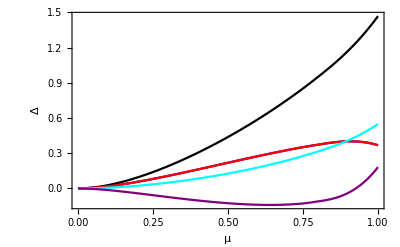

```mathematica
deltanewdiscordmuint=Interpolation[DAtoBtoCW];
D2ABmuint=Interpolation[ΔAtoBgivenCW];
D2ACmuint=Interpolation[ΔAtoBgivenCW];
D3muint=Interpolation[ΔAtoBtoCW];
discordBtoCmuint=Interpolation[ΔBtoCgivenπW];
Plot[{deltanewdiscordmuint[x],D2ABmuint[x],D2ACmuint[x],discordBtoCmuint[x],D3muint[x]},{x,0,1},PlotStyle->{Black,Blue,Red,Cyan,Purple},PlotRange->All,Frame->True ,FrameLabel->{"μ","Δ"},FrameStyle->Black,FrameLabel->{Style["μ",20,Bold],Style["Δ",20,Bold]},LabelStyle->Directive[Bold, Medium],Axes->False]
```

Werner W Experimental with Theoretical Theta

```mathematica
DAtoBtoCWexp1={{0.,0.006752635981230881},{0.1,0.027223118894079468},{0.2,0.08189664836351285},{0.3,0.16078583479173703},{0.4,0.25940546962350197},{0.5,0.3757443959374531},{0.6,0.5094854014367474},{0.7,0.6620463948894875},{0.8,0.8376044809572196},{0.9,1.0472829473275505},{1.,1.3278751181769883 }};
ΔAtoBgivenCWexp1={{0.,0.0035090583872325887},{0.1,0.011806443172491132},{0.2,0.03723690474353236},{0.3,0.07224772448560368},{0.4,0.11286144792412234},{0.5,0.15671954522697518},{0.6,0.20217975004004352},{0.7,0.24788822448312775},{0.8,0.29253161634406344},{0.9,0.334903135000838},{1.,0.3884582180584647}};
ΔAtoCgivenBWexp1={{0.,0.004502066120978476},{0.1,0.015271634680492863},{0.2,0.04557050641610627},{0.3,0.08656257517333632},{0.4,0.1339864450972894},{0.5,0.18526097788863005},{0.6,0.2385639923768661},{0.7,0.2924048747923724},{0.8,0.34542164034837186},{0.9,0.3967102628270416},{1.,0.4630896517856723}};
ΔBtoCgivenπWexp1={{0.,0.0016495577816240115},{0.1,0.009396653650432851},{0.2,0.026607570435957406},{0.3,0.05194920860573515},{0.4,0.0849885434249702},{0.5,0.1257860291554158},{0.6,0.17492686983161554},{0.7,0.23375045949285878},{0.8,0.3050300980215517},{0.9,0.3953213221087708},{1.,0.5099518697314085}};
ΔAtoBtoCWexp1={{0.,-0.0029080463086043062},{0.1,-0.009251612609337379},{0.2,-0.027518333232083192},{0.3,-0.04997367347293835},{0.4,-0.07243096682288008},{0.5,-0.0920221563335677},{0.6,-0.1061852108117779},{0.7,-0.11199716387887126},{0.8,-0.10537887375676736},{0.9,-0.07965177260909995},{1.,-0.033624621398557264}};
```

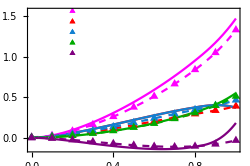

```mathematica
deltanewdiscordmuintWexp1=Interpolation[DAtoBtoCWexp1];
D2ABmuintWexp1=Interpolation[ΔAtoBgivenCWexp1];
D2ACmuintWexp1=Interpolation[ΔAtoCgivenBWexp1];
D3muintWexp1=Interpolation[ΔAtoBtoCWexp1];
discordBtoCmuintWexp1=Interpolation[ΔBtoCgivenπWexp1];
plt1=Plot[{deltanewdiscordmuint[x],D2ABmuint[x],D2ACmuint[x],discordBtoCmuint[x],D3muint[x](*,deltanewdiscordmuintWexp1[x],D2ABmuintWexp1[x],D2ACmuintWexp1[x],discordBtoCmuintWexp1[x],D3muintWexp1[x]*)},{x,0,1},PlotStyle->{Magenta,Red,RGBColor[0.07,0.5,0.82],Darker[Green],Purple},PlotRange->All,Frame->True ,FrameStyle->Black ,TicksStyle->{{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"},{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"}},Axes->False];
plt101=ListPlot[{{0.20,1.56}},PlotStyle->{Magenta},PlotMarkers->{"▲",7},Axes->False,Frame->False,PlotRange->All];
plt102=ListPlot[{{0.20,1.43}},PlotStyle->{Red},PlotMarkers->{"▲",7},Axes->False,Frame->False,PlotRange->All];
plt103=ListPlot[{{0.20,1.30}},PlotStyle->{RGBColor[0.07,0.5,0.82]},PlotMarkers->{"▲",7},Axes->False,Frame->False,PlotRange->All];
plt104=ListPlot[{{0.20,1.17}},PlotStyle->{Darker[Green]},PlotMarkers->{"▲",7},Axes->False,Frame->False,PlotRange->All];
plt105=ListPlot[{{0.20,1.04}},PlotStyle->{Purple},PlotMarkers->{"▲",7},Axes->False,Frame->False,PlotRange->All];
plt2=Plot[{(*deltanewdiscordmuint[x],D2ABmuint[x],D2ACmuint[x],discordBtoCmuint[x],D3muint[x],*)deltanewdiscordmuintWexp1[x],D2ABmuintWexp1[x],D2ACmuintWexp1[x],discordBtoCmuintWexp1[x],D3muintWexp1[x]},{x,0,1},PlotStyle->{(*Magenta,Red,RGBColor[0.07,0.5,0.82],Darker[Green],Purple,*){Magenta,Dashed},{ Red,Dashed}, {RGBColor[0.07,0.5,0.82],Dashed},{Darker[Green],Dashed},{Purple,Dashed}},PlotRange->All,Frame->True ,FrameStyle->Black,FrameLabel->{Style["μ",10,Thickness[0.010]],Style["Δ",10,Thickness[0.010]]},TicksStyle->{{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"},{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"}},Axes->False];
plt3=ListPlot[{DAtoBtoCWexp1,ΔAtoBgivenCWexp1,ΔAtoCgivenBWexp1, ΔBtoCgivenπWexp1, ΔAtoBtoCWexp1},PlotStyle->{Magenta,Red,RGBColor[0.07,0.5,0.82],Darker[Green],Purple},PlotMarkers->{" ▲", 10},PlotRange->All,Frame-> True,FrameStyle->Black,TicksStyle->{{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"},{Directive[Black,25,Thickness[0.010]],FontFamily->"LM Roman Caps 10"}},Axes->False];
Show[{plt1,plt2,plt3, plt101, plt102, plt103, plt104, plt105},AspectRatio->2/3,ImageSize->250]
```